```mathematica
RSolve[{a[1]==1,a[2]==1,a[3]==1,a[n+3]==a[n+2]+ a[n+1]+ a[n]},a[n],n]
```

{{a[n]→(Root1.84Root[-1-#1-#1^2+#1^3&,1]1.8392867552141612)^n Root0.237Root[-1+#1+11 #1^2+11 #1^3&,1]0.2368398446387851+(Root-0.420+0.606 ⅈRoot[-1-#1-#1^2+#1^3&,3]-0.4196433776070806)^n Root-0.618-0.0374 ⅈRoot[-1+#1+11 #1^2+11 #1^3&,2]-0.6184199223193926+(Root-0.420-0.606 ⅈRoot[-1-#1-#1^2+#1^3&,2]-0.4196433776070806)^n Root-0.618+0.0374 ⅈRoot[-1+#1+11 #1^2+11 #1^3&,3]-0.6184199223193926}}

```mathematica
Clear[n]
```

```mathematica
di2=(Sqrt[2])^(Log[n]);
di4 = (n+2)!;

di1=n^(2/Log[n]);
di3=0.2*n^(Sqrt[2]);
di5=n^n;
```

```mathematica
di1/di2
```

2^(-Log[n]/2) n^(2/Log[n])

```mathematica
Simplify[2^(-Log[n]/2) n^(2/Log[n])]
```

ⅇ^(2-1/2 Log[2] Log[n])

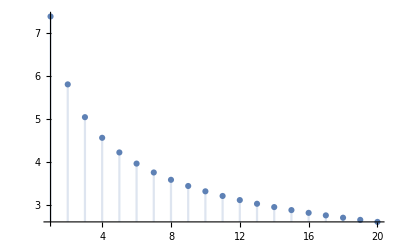

```mathematica
DiscretePlot[ⅇ^(2-1/2 Log[2] Log[n]),{n,1,20}]
```

```mathematica
2^(-(Log n)/2) n^(2/(Log n))
```

2^(-(Log n)/2) n^(2/(Log n))

```mathematica
Limit[((n+2)!)/n^n,n->Infinity]
```

0

```mathematica
Limit[(0.2*n^(Sqrt[2]))/((n+2)!),n->Infinity]
```

0.

```mathematica
Limit[(0.2*n^(Sqrt[2]))/((n+2)!),n->Infinity]
```

0.

```mathematica
Limit[(Sqrt[2])^(Log[n])/(0.2*n^(Sqrt[2])),n->Infinity]
```

0.

```mathematica
Limit[n^(2/Log[n])/(Sqrt[2])^(Log[n]),n->Infinity]
```

0

```mathematica
RSolve[{a[1]==d,a[n]==16*a[n/2]+ (n+1)(n+2)+c},a[n],n]
RSolve[{a[1]==d,a[n]==8*a[n/2]+ (n+1)(n+2)+c},a[n],n]
RSolve[{a[1]==d,a[n]==4*a[n/2]+ (n+1)(n+2)+c},a[n],n]
RSolve[{a[1]==d,a[n]==2*a[n/2]+ (n+1)(n+2)+c},a[n],n]
RSolve[{a[1]==d,a[n]==a[n/2]+ (n+1)(n+2)+c},a[n],n]
```

{{a[n]→1/105 (-14-7 c-45 n-35 n^2+94 n^4+7 c n^4+105 d n^4)}}

{{a[n]→1/7 (-2-c-7 n-7 n^2+16 n^3+c n^3+7 d n^3)}}

{{a[n]→1/3 (-2-c-9 n+11 n^2+c n^2+3 d n^2+(3 n^2 Log[n])/Log[2])}}

{{a[n]→-2-c+c n+d n+2 n^2+(3 n Log[n])/Log[2]}}

{{a[n]→1/3 (-22+3 d+18 n+4 n^2+(6 Log[n])/Log[2]+(3 c Log[n])/Log[2])}}

```mathematica
105/7
```

15

```mathematica
9^(1/3)
```

3^(2/3)

```mathematica
N[3^(2/3)]
```

2.08008

```mathematica
N[3^(1/3)]
```

1.44225

```mathematica
Root[-1 - #1 - #1^2 + #1^3 & , 3, 0]
```

Root-0.420+0.606 ⅈRoot[-1-#1-#1^2+#1^3&,3]-0.4196433776070806

```mathematica
N[Root[-1-#1-#1^2+#1^3&,3,0]]
```

-0.419643+0.606291 ⅈ

```mathematica
Abs[-0.4196433776070806+0.6062907292071994 ⅈ]
```

0.737353

```mathematica
RSolve[{a[1]==c,a[n]==2*a[n/4]+Log[n]+Sqrt[n]+d},a[n],n]
```

{{a[n]→2^(Log[n]/Log[4]) c-d+2^(Log[n]/Log[4]) d-2 Log[4]+2^(1+Log[n]/Log[4]) Log[4]-Log[n]+(√(2^((2 Log[n])/Log[4])) Log[n])/Log[4]}}

```mathematica
a[n_]:=-c+2^(Log[n]/Log[4]) c+2^(Log[n]/Log[4]) d-4 Log[4]+2^(2+Log[n]/Log[4]) Log[4]-2 Log[n]+(√(2^((2 Log[n])/Log[4])) Log[n])/Log[4]
```

```mathematica
2^(1+Log[n]/Log[4])
```

2^(1+Log[n]/Log[4])

```mathematica
Simplify[2^(1+Log[n]/Log[4])]
```

2^(Log[4 n]/Log[4])

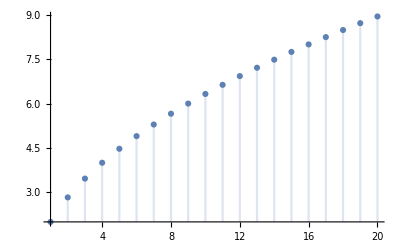

```mathematica
DiscretePlot[2^(Log[4 n]/Log[4]),{n,1,20}]
```

```mathematica
Limit[1/(Sqrt[n]*Log[n])(2^(Log[n]/Log[4]) c-d+2^(Log[n]/Log[4]) d-2 Log[4]+2^(1+Log[n]/Log[4]) Log[4]-Log[n]+(√(2^((2 Log[n])/Log[4])) Log[n])/Log[4]),n->Infinity]
```

1/Log[4]

```mathematica
Limit[(2Log[n]+Sqrt[n])/Sqrt[n],n->Infinity]
```

1

```mathematica
Solve[x^3-x^2-x-1==0]
```

{{x→Root1.84Root[-1-#1-#1^2+#1^3&,1]1.8392867552141612},{x→Root-0.420-0.606 ⅈRoot[-1-#1-#1^2+#1^3&,2]-0.4196433776070806},{x→Root-0.420+0.606 ⅈRoot[-1-#1-#1^2+#1^3&,3]-0.4196433776070806}}

```mathematica
Last[{{x->Root[-1-#1-#1^2+#1^3&,1,0]},{x->Root[-1-#1-#1^2+#1^3&,2,0]},{x->Root[-1-#1-#1^2+#1^3&,3,0]}}]
```

2     3
{x -> Root[-1 - #1 - #1  + #1  & , 3, 0]}

```mathematica
First[{{x->Root[-1-#1-#1^2+#1^3&,1,0]},{x->Root[-1-#1-#1^2+#1^3&,2,0]},{x->Root[-1-#1-#1^2+#1^3&,3,0]}}]
```

{x→Root1.84Root[-1-#1-#1^2+#1^3&,1]1.8392867552141612}

```mathematica
x/.{x->Root[-1-#1-#1^2+#1^3&,1,0]}
```

Root1.84Root[-1-#1-#1^2+#1^3&,1]1.8392867552141612

```mathematica
x/.{x->Root[-1-#1-#1^2+#1^3&,1,0]}
```

Root1.84Root[-1-#1-#1^2+#1^3&,1]1.8392867552141612

```mathematica
Abs[0.4+0.6I]
```

0.72111

```mathematica
Root"1.84"Root[-1-#1-#1^2+#1^3&,1]1.8392867552141612
```

2     3
Root[-1 - #1 - #1  + #1  & , 1, 0]

```mathematica
ToRadicals[Root[-1-#1-#1^2+#1^3&,1,0]]
```

1/3 (1+(19-3 √33)^(1/3)+(19+3 √33)^(1/3))

```mathematica
RootReduce[1/3 (1+(19-3 √33)^(1/3)+(19+3 √33)^(1/3))]
```

Root1.84Root[-1-#1-#1^2+#1^3&,1]1.8392867552141612

```mathematica
N[1/3 (1+(19-3 √33)^(1/3)+(19+3 √33)^(1/3))]
```

1.83929

```mathematica
MinimalPolynomial[Root[-1-#1-#1^2+#1^3&,1,0],x]
```

-1-x-x^2+x^3

```mathematica
FullSimplify[-1-x-x^2+x^3]
```

-1+x (-1+(-1+x) x)

```mathematica
Root[-1-#1-#1^2+#1^3&,2,0]
```

Root-0.420-0.606 ⅈRoot[-1-#1-#1^2+#1^3&,2]-0.4196433776070806

```mathematica
ToRadicals[Root[-1-#1-#1^2+#1^3&,3,0]]
```

```mathematica
1/3-1/6 (1+ⅈ √3) (19-3 √33)^(1/3)-1/6 (1-ⅈ √3) (19+3 √33)^(1/3)
```

1/3-1/6 (1+ⅈ √3) (19-3 √33)^(1/3)-1/6 (1-ⅈ √3) (19+3 √33)^(1/3)

```mathematica
N[1/3-1/6 (1+ⅈ √3) (19-3 √33)^(1/3)-1/6 (1-ⅈ √3) (19+3 √33)^(1/3)]
```

-0.419643+0.606291 ⅈ

```mathematica
RSolve[{a[1]==1,a[n]==n^2+281*a[n/3]},a[n],n]
```

{{a[n]→1/272 (-9^(1+Log[n]/Log[3])+281^(1+Log[n]/Log[3]))}}

```mathematica
Limit[(1/272 (-9^(1+Log[n]/Log[3])+281^(1+Log[n]/Log[3])))/n^(Log[3,281]),n->Infinity]
```

281/272

```mathematica
10*10*10000
```

1000000

```mathematica
Log[3,281]
```

Log[281]/Log[3]